## Fitnesses

```mathematica
θ[x_,thresh_]:=If[x<thresh,0,1];
V[S_,p_,q_,r_,k_]:=Binomial[S-1,k] (p/(1-r))^k(q/(1-r))^(S-1-k);

πD[b_,num_,thresh_]:=b θ[num,thresh]+1;
πC[b_,c_,num_,thresh_]:=πD[b,num,thresh]-c/num  θ[num,thresh]-c/thresh (1-θ[num,thresh]);

πintraD[d_,b_,c_,num_,ω_]:=b/d∑_(i=0)^(num-1) ω^i;
πintraC[d_,b_,c_,num_,ω_]:=πintraD[d,b,c,num,ω]-c;

PintraD[S_,p_,q_,r_,d_,b_,c_,ω_]:=∑_(k=0)^(S-1) V[S,p,q,r,k]πintraD[d,b,c,k,ω];
PinterD[S_,p_,q_,r_,b_,thresh_]:=∑_(k=0)^(S-1) V[S,p,q,r,k]πD[b,k,thresh];
PintraC[S_,p_,q_,r_,d_,b_,c_,ω_]:=∑_(k=0)^(S-1) V[S,p,q,r,k]πintraC[d,b,c,k+1,ω];
PinterC[S_,p_,q_,r_,b_,thresh_]:=∑_(k=0)^(S-1) V[S,p,q,r,k]πC[b,c,k+1,thresh];


fD[d_,dintra_,x1_,x2_,z1_,y1_,y2_,z2_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(S=2)^(d-1) (Binomial[d-1,S-1] (1-z2)^(S-1) z2^(d-S) PinterD[S,y1,y2,z2,b,thresh]))+(1-p)(∑_(S=2)^(dintra-1) (Binomial[dintra-1,S-1] (1-z1)^(S-1) z1^(d-S) PintraD[S,x1,x2,z1,dintra,bintra,cintra,ω]));



fC[d_,dintra_,x1_,x2_,z1_,y1_,y2_,z2_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(S=2)^(d-1) (Binomial[d-1,S-1] (1-z2)^(S-1) z2^(d-S) PinterC[S,y1,y2,z2,b,thresh]))+(1-p)(∑_(S=2)^(dintra-1) (Binomial[dintra-1,S-1] (1-z1)^(S-1) z1^(d-S) PintraC[S,x1,x2,z1,dintra,bintra,cintra,ω]));
```

## Dynamics

```mathematica
g1dot[d_,dintra_,g1_,z1_,g2_,z2_,b_,c_,bintra_,cintra_,thresh_,m_,ω_,p_]:=m  z1 g1(1−g1)(fC[d,dintra,g1 (1-z1),(1-g1 )(1-z1),z1,g2 (1-z2),(1-g2)(1-z2),z2,b,c,bintra,cintra,thresh,ω,p]−fD[d,dintra,g1 (1-z1),(1-g1 )(1-z1),z1,g2 (1-z2),(1-g2)(1-z2),z2,b,c,bintra,cintra,thresh,ω,p]);
g2dot[d_,dintra_,g1_,z1_,g2_,z2_,b_,c_,bintra_,cintra_,thresh_,n_,ω_,p_]:=n  z2 g2(1−g2)(fC[d,dintra,g2 (1-z2),(1-g2)(1-z2),z2,g1 (1-z1),(1-g1 )(1-z1),z1,b,c,bintra,cintra,thresh,ω,p]−fD[d,dintra,g2 (1-z2),(1-g2)(1-z2),z2,g1 (1-z1),(1-g1 )(1-z1),z1,b,c,bintra,cintra,thresh,ω,p]);

z1dot[d_,dintra_,g1_,z1_,g2_,z2_,b_,c_,bintra_,cintra_,thresh_,m_,ω_,p_,e1_]:=m e1(1−z1)−m z1(1−z1)(g1 fC[d,dintra,g1 (1-z1),(1-g1 )(1-z1),z1,g2 (1-z2),(1-g2)(1-z2),z2,b,c,bintra,cintra,thresh,ω,p]−(1−g1)fD[d,dintra,g1 (1-z1),(1-g1 )(1-z1),z1,g2 (1-z2),(1-g2)(1-z2),z2,b,c,bintra,cintra,thresh,ω,p]);
z2dot[d_,dintra_,g1_,z1_,g2_,z2_,b_,c_,bintra_,cintra_,thresh_,n_,ω_,p_,e2_]:=n e2(1−z2)−n z2(1−z2)(g2 fC[d,dintra,g2 (1-z2),(1-g2)(1-z2),z2,g1 (1-z1),(1-g1 )(1-z1),z1,b,c,bintra,cintra,thresh,ω,p]−(1−g2)fD[d,dintra,g2 (1-z2),(1-g2)(1-z2),z2,g1 (1-z1),(1-g1 )(1-z1),z1,b,c,bintra,cintra,thresh,ω,p])


res[p_,q_,r_,s_,lim_]:=Quiet[NDSolve[{
g1'[t]== m  z1[t] g1[t](1−g1[t])(fC[d1,d1intra,g1[t] (1-z1[t]),(1-g1[t])(1-z1[t]),z1[t],g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob[t]]−fD[d1,d1intra,g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob[t]]),
g2'[t]== n  z2[t] g2[t](1−g2[t])(fC[d2,d2intra,g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob[t]]−fD[d2,d2intra,g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob[t]]),
z1'[t]== m e1(1−z1[t])−m z1[t](1−z1[t])(g1[t] fC[d1,d1intra,g1[t] (1-z1[t]),(1-g1[t])(1-z1[t]),z1[t],g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob[t]]−(1−g1[t])fD[d1,d1intra,g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob[t]]),
z2'[t]== n e2(1−z2[t])−n z2[t](1−z2[t])(g2[t] fC[d2,d2intra,g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob[t]]−(1−g2[t])fD[d2,d2intra,g2[t] (1-z2[t]),(1-g2[t])(1-z2[t]),z2[t],g1[t] (1-z1[t]),(1-g1[t] )(1-z1[t]),z1[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob[t]]),
g1[0]==p,g2[0]==q,z1[0]==r,z2[0]==s},{g1,g2,z1,z2},{t,lim}]];
(*liseval[t_,rep_]:=Evaluate[{x[t],y[t]}/.rep];*)

gamea={3,3/4};
gameb={1,3/4};
gamec={1,4/3};
gamed={3,4/3};

d1=5;
d2=5;
d1intra=5;
d2intra=5;
thresh1=1;
thresh2=1;
b=2;
c=1;
bintraforsp1=10;
cintraforsp1=gameb⟦1⟧;
ωforsp1=gameb⟦2⟧//N;

bintraforsp2=10;
cintraforsp2=gameb⟦1⟧;
ωforsp2=gameb⟦2⟧//N;

m=1/8//N;
n=1;
e1=0.05;
e2=0.05;

a=0.1;
prob[t_]:=0.666 (*(Sin[a t]+1)/2*) ;
lim=8000;
```

```mathematica
Manipulate[{
ParametricPlot[Evaluate[{z1[time],g1[time]}/.res[p,q,r,s,lim]],{time,0,lim},PlotRange->{{-0.02,1.02},{-0.02,1.02}},AspectRatio->1,Frame->True],
ParametricPlot[Evaluate[{z2[time],g2[time]}/.res[p,q,r,s,lim]],{time,0,lim},PlotRange->{{-0.02,1.02},{-0.02,1.02}},AspectRatio->1,Frame->True]},{{p,0.85},0,1,AngularGauge[##1,ImageSize->100,GaugeLabels->"g_1",PlotLabel->"Fraction Generous"]&},
{{q,0.5},0,1,AngularGauge[##1,ImageSize->100,GaugeLabels->"g_2"]&},
{{r,0.2},0,1,AngularGauge[##1,ImageSize->100,GaugeLabels->"z_1",PlotLabel->"Empty Spaces"]&},
{{s,0.5},0,1,AngularGauge[##1,ImageSize->100,GaugeLabels->"z_2"]&},ControlPlacement->{Left,Left,Right,Right}]
```

```mathematica
lim=9000;
biglissp1={};
colourlistsp1={};
lastlist={};
For[u=0.05,u≤0.95,u=u+0.05,
For[v=0.05,v≤0.95,v=v+0.05,
lis=Flatten[Table[Evaluate[{z1[time],g1[time]}/.res[v,0.5,u,0.5,lim]],{time,0,lim}],1];
AppendTo[biglissp1,lis];
last=Evaluate[{z1[lim],g1[lim]}/.res[v,0.5,u,0.5,lim]];
AppendTo[lastlist,SetAccuracy[Last[lis]//Chop,4]];
If[last⟦1⟧⟦1⟧>0.99,AppendTo[colourlistsp1,Black]];
If[last⟦1⟧⟦2⟧>0.99,AppendTo[colourlistsp1,Blue]];
If[last⟦1⟧⟦1⟧<0.99&&last⟦1⟧⟦2⟧<0.99,AppendTo[colourlistsp1,cols⟦2⟧]];
]
]
```

```mathematica
cols=Short[ColorData[24,"ColorList"],4]⟦1⟧
```

```mathematica
biglissp1//Dimensions
```

{361,9001,2}

```mathematica
shortlist1=Take[#,{1,9001,10}]&/@biglissp1;
```

```mathematica
list1pl=ListPlot[shortlist1,Joined->True,AspectRatio->1,PlotStyle->colourlistsp1]
```

-Graphics-

```mathematica
ptstopl=Tally[SetAccuracy[lastlist,2]]⟦All,1⟧;
```

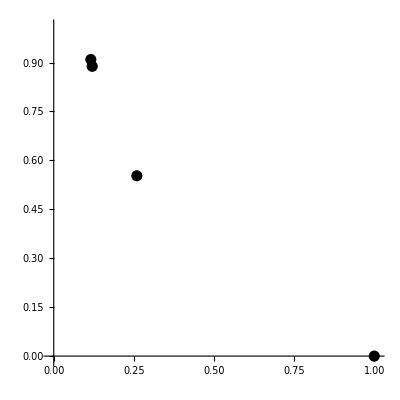

```mathematica
fp1=ListPlot[ptstopl,Joined->False,PlotRange->{{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,PlotStyle->Directive[Black,PointSize[0.02]]]
```

```mathematica
lim=9000;
blacklistsp1={{0,0}};
bluelistsp1={{0,0}};
greenlistsp1={{0,0}};
For[u=0.01,u≤0.99,u=u+0.01,
For[v=0.01,v≤0.99,v=v+0.01,
last=Evaluate[{z1[lim],g1[lim]}/.res[v,0.5,u,0.5,lim]];
AppendTo[lastlist,last];
If[last⟦1⟧⟦1⟧>0.99,AppendTo[blacklistsp1,{u,v}]];
If[last⟦1⟧⟦2⟧>0.99,AppendTo[bluelistsp1,{u,v}]];
If[last⟦1⟧⟦1⟧<0.99&&last⟦1⟧⟦2⟧<0.99,AppendTo[greenlistsp1,{u,v}]];
]
]
```

```mathematica
detailedplot1=ListPlot[{blacklistsp1,bluelistsp1,greenlistsp1},PlotStyle->{Black,Blue,cols⟦2⟧},AspectRatio->1,PlotRange->{{-0.02,1.02},{-0.02,1.02}}];
```

```mathematica
Show[detailedplot1,list1pl,fp1,Frame->True,FrameStyle->Thickness[0.004],ImagePadding->20]
```

-Graphics-

```mathematica
lim=9000;
biglissp2={};
colourlistsp2={};
lastlist2={};
For[u=0.05,u≤0.95,u=u+0.05,
For[v=0.05,v≤0.95,v=v+0.05,
lis=Flatten[Table[Evaluate[{z2[time],g2[time]}/.res[0.6,v,0.6,u,lim]],{time,0,lim}],1];
AppendTo[biglissp2,lis];
last=Evaluate[{z2[lim],g2[lim]}/.res[0.6,v,0.6,u,lim]];
AppendTo[lastlist2,last];
If[last⟦1⟧⟦1⟧>0.99,AppendTo[colourlistsp2,Black]];
If[last⟦1⟧⟦2⟧>0.99,AppendTo[colourlistsp2,Blue]];
If[last⟦1⟧⟦1⟧<0.99&&last⟦1⟧⟦2⟧<0.6,AppendTo[colourlistsp2,cols⟦2⟧]];
]
]
```

```mathematica
shortlist2=Take[#,{1,9001,2}]&/@biglissp2;
```

```mathematica
list2pl=ListPlot[shortlist2,Joined->True,AspectRatio->1,PlotStyle->colourlistsp2]
```

-Graphics-

```mathematica
ptstopl2=Tally[SetAccuracy[lastlist2,2]]⟦All,1⟧;
```

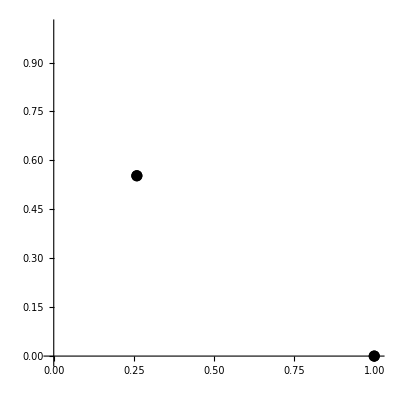

```mathematica
fp2=ListPlot[ptstopl2,Joined->False,PlotRange->{{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,PlotStyle->Directive[Black,PointSize[0.02]]]
```

```mathematica
lim=9000;
blacklistsp2={{0,0}};
bluelistsp2={{0,0}};
greenlistsp2={{0,0}};
For[u=0.01,u≤0.99,u=u+0.01,
For[v=0.01,v≤0.99,v=v+0.01,
last=Evaluate[{z2[lim],g2[lim]}/.res[0.6,v,0.6,u,lim]];
If[last⟦1⟧⟦1⟧>0.99,AppendTo[blacklistsp2,{u,v}]];
If[last⟦1⟧⟦2⟧>0.99,AppendTo[bluelistsp2,{u,v}]];
If[last⟦1⟧⟦1⟧<0.99&&last⟦1⟧⟦2⟧<0.99,AppendTo[greenlistsp2,{u,v}]];
]
]
```

```mathematica
detailedplot2=ListPlot[{blacklistsp2,bluelistsp2,greenlistsp2},PlotStyle->{Black,Blue,cols⟦2⟧},AspectRatio->1,PlotRange->{{-0.02,1.02},{-0.02,1.02}}];
```

```mathematica
Show[detailedplot2,list2pl,fp2,Frame->True,FrameStyle->Thickness[0.004],ImagePadding->20,PlotRange->{{-0.02,1.02},{-0.02,1.02}}]
```

-Graphics-